## Fisher information in antigen level (general case)

Calculate FI in n_ag in the presence of rebinding and force-sharing. We first establish coupled equation from which one can obtain the mean and variance of n_ag. Then we calculate the lower bound of FI based on Eq.S51 in SI.

### 1. Define some utility functions

```mathematica
(*====================================*)
(*delta function*)
Delta[m_, n_]:=DiscreteDelta[m-n]
(*theta step function*)
Theta[m_, m0_:0]:=UnitStep[m-m0]
(*translate function*)
(*translate coordinate (m, n) into 1D index*)
Trans[m_, n_]:=m*(N0+1)+n+1
(*translate back from 1D index to (m, n)*)
BackTrans[ii_]:= {IntegerPart[Max[(ii-1)/(N0+1),0]], Mod[ii-1, N0+1]}

(*force function*)
Kf[m_, F_,f_]:=If[m==0,0,Exp[F/(m f)]];
(*===================================*)
```

### 2. Specify parameters

```mathematica
Clear[k1off, k2off, k1on, k2on, N0, m, t, n, x,F,f1,f2]
k1off = 1; (*APC-Ag off rate*)
k2off=1;(*BCR-Ag off rate*)
kon=1;(*on rate*)
k1on = 0; (*APC-Ag on rate*)
k2on = k1on;(*BCR-Ag on rate*)
F=10;(*force, pN*)
f1=4012/1500;(*kT / bond length of APC-Ag, pN*)
f2=4012/2000;(*kT / bond lenght of BCR-Ag, pN*)
N0 = 20;(*cluster size*)
```

### 3. Calculate the exact antigen level distribution.

Here we calculate the exact antigen level distribution P(n). It can be used to validate our calculation of mean and variance later.

```mathematica
N0=10;
Clear[solverN, solver]
Clear[k2off, F, koon, check, k1off, f1, f2]
(*Calculate the probability distribution of n_ag: P(nag)*)
solverN[k2off_, F_, kon_, check_:False]:=Module[{
threshold=10^(-4),
 k1off=1,
f1=4012/1500,
f2=4012/2000
},
(*If F=0, the distribution is Binomial*)
(*Otherwise, we need to solve the linear equations about Qmn*)
If[Abs[F]<threshold,
PTable=Table[{i,N[Binomial[N0, i]k1off^i k2off^(N0-i)/(k1off+k2off)^N0]},{i,0,N0}],
PTable =solver[k2off, F, kon, k1off, f1, f2, check, simplify=False]];
(*Check the total probability*)
If[Abs[Sum[PTable[[i, 2]],{i,1, N0+1}]-1]>threshold, Print["total probability not equal 1, sum=", Sum[PTable[[i, 2]],{i,1, N0+1}]]];
PTable
]
```

The following solver calculates the probability distribution of n_ag by solving linear equations of Qmn

```mathematica
solver[k2off_, F_, kon_, k1off_, f1_, f2_, check_:False, simplify_:True]:=Module[{},

(*The function DecodeEntryN calculates the transition rate from state (m1,n1) to (m2,n2) based on the equation of Qmn.*)
Clear[DecodeEntryN];
DecodeEntryN[m1_,n1_, m2_, n2_]:=
(k1off Kf[m1+1, F, f1] * (m1+1)Delta[m1+1, m2]Delta[n1-1, n2]Theta[n1-1]Theta[N0, m1+1]+
k2off Kf[m1+1, F, f2]*(m1+1)Delta[m1+1, m2]Delta[n1,n2]Theta[N0, m1+1]+
kon*(n1+1)Delta[m1-1,m2]Delta[n1+1, n2]Theta[m1-1,1]Theta[N0, n1+1]+
kon*(N0-m1-n1+1)Delta[m1-1, m2]Delta[n1, n2]Theta[m1-1,1]-
(k1off Kf[m1, F, f1]*m1+k2off Kf[m1, F, f2]*m1 + (N0-m1)*kon)Delta[m1,m2]Delta[n1,n2])Theta[N0, m1+n1]Theta[N0, m2+n2]Theta[m2,1]Theta[m1,1];

(*We then convert the transition matrix in (m,n) space into the 1D index space.The following function denotes the transition rate from state ii to state jj.*)
Clear[EntryN];
EntryN[ii_, jj_]:=
DecodeEntryN[BackTrans[ii][[1]], BackTrans[ii][[2]], BackTrans[jj][[1]], BackTrans[jj][[2]]];


(*Use EntryN to establish the transition matrix for Qmn*)
Clear[A];
A = Table[0, {i,(N0+1)^2}, {j,(N0+1)^2}];
For[i=1, i<(N0+1)^2+1,i++,{
For[j=1, j<(N0+1)^2+1, j++, {
A[[i, j]] = EntryN[i, j]
}]
}];

(*Initialize state vector*)
Clear[x,t,i];
X = Table[x[i], {i, (N0+1)^2}];

(*vec b*)
Clear[B];
B= Table[0,{i,(N0+1)^2}];
B[[Trans[N0, 0]]]=-1;

(*In the following we will solve the linear system A*X = B *)
Clear[system];
system={A.X==B};

(*solve the linear system*)
Clear[sol];
If[ NumberQ[k2off],If[IntegerQ[k2off], sol=LinearSolve[A, B],
sol=LinearSolve[A, B, Method->"Multifrontal"]], sol=LinearSolve[A, B]];

(*load the solution*)
Clear[Q1Table,PTable];
Q1Table = Table[If[simplify, Simplify[sol[[Trans[1, i]]]], sol[[Trans[1, i]]]], {i, 0 ,N0}];

(*Extract P(n) from the solution of Qmn*)
PTable = Table[{i-1, k1off Kf[1,F,f1]*Q1Table[[i-1]]*Theta[i, 2]+k2off  Kf[1,F,f2]*Q1Table[[i]]*Theta[N0, i]},{i, 1, N0+1}];

If[check, Print["P Table=", PTable]];
If[check,
{Print["prob. table=", PTable];
Print["binomal tab=", Table[N[Binomial[N0, i]k1off^i k2off^(N0-i)/(k1off+k2off)^N0],{i,0,N0}]];
Print["no-rebind mean=", Sum[k1off Kf[i, F, f1]/(k2off Kf[i, F, f2]+k1off Kf[i, F, f1]),{i,1, N0}],
", calculated mean=",Sum[(i-1)*PTable[[i, 2]],{i,1, N0+1}] ];
Print["no-rebind std=", Sqrt[Sum[k1off Kf[i, F, f1] k2off Kf[i, F, f2]/(k2off Kf[i, F, f2]+k1off Kf[i, F, f1])^2,{i,1, N0}]],
", calculated std=", Sqrt[Sum[(i-1)^2*PTable[[i, 2]],{i,1, N0+1}]-Sum[(i-1)*PTable[[i, 2]],{i,1, N0+1}]^2]];
}
];
(*calculate the mean*)
Clear[nMean, nStd];
nMean = Sum[(i-1)*PTable[[i,2]],{i,1,N0+1}];
nStd = Sqrt[Sum[(i-1)^2*PTable[[i,2]],{i,1,N0+1}]-nMean^2];

(*return the mean and std*)
(*{nMean, nStd}*)
PTable
]
```

```mathematica
N0=10;
dis = solverN[1*Exp[0.01], 10, 1.0]
```

{{0,0.00500737},{1,0.0354368},{2,0.112146},{3,0.208848},{4,0.253243},{5,0.208701},{6,0.118226},{7,0.045383},{8,0.0112731},{9,0.0016315},{10,0.00010404}}

### 4. Calculate the mean antigen level

```mathematica
N0=3; (*Use a small number for testing*)
Clear[findNMean];
findNMean[k2off_, F_, kon_, check_:False]:=Module[{
(*constant parameter*)
threshold=10^(-4),
k1off=1,
f1=4012/1500,
f2=4012/2000
},

Clear[rm, sm, gm];
rm[m_]:=m k1off Exp[F /(m f1)]; (*APC-Ag off propensity*)
sm[m_]:=m k2off Exp[F/(m f2)]; (*BCR-Ag off propensity*)
gm[m_]:=kon (N0-m); (*on propensity*)

(*calculate Rm0*)
Clear[fmTable];
fmTable =Table[0, {i, N0}];
fmTable[[1]] = 1/(rm[1]+sm[1]);
fmTable[[2]] = (1+kon (N0-1)/(rm[1]+sm[1]))/(rm[2]+sm[2]);
For[i=3,i<=N0, i++,
fmTable[[i]] = ((rm[i-1]+sm[i-1]+gm[i-1])fmTable[[i-1]]-gm[i-2]fmTable[[i-2]])/(rm[i]+sm[i])
];

(*calculate Rm1*)
(*The linear equations about Rm1 is a tridiagonal system*)
(*I borrowed the method from stack-overflow: https://mathematica.stackexchange.com/questions/20921/solving-a-tridiagonal-system-of-linear-equations-using-the-thomas-algorithm*)
Clear[amTable, bmTable,cmTable, dmTable];
amTable = Table[gm[m1]Theta[m1-1, 1],{m1, 1, N0-1}];
bmTable = Table[-(rm[m1]+sm[m1]+gm[m1]),{m1, 1, N0-1}];
cmTable = Table[(rm[m1+1]+sm[m1+1])Theta[N0-1, m1+1],{m1, 1, N0-1}];
dmTable = Table[-rm[i+1]fmTable[[i+1]],{i,N0-1}];

Clear[cPrime, dPrime, xOut];
cPrime[x_,{ax_,bx_,cx_}]:=cx/(bx-x ax);
dPrime[x_,{ax_,bx_,cpx_,dx_}]:=(dx-x ax)/(bx-cpx ax);
xOut[x_,{cpx_,dpx_}]:=dpx-x cpx;

Clear[cp, dp, out, triThomas];
cp=Rest[FoldList[cPrime,cmTable[[1]]/bmTable[[1]],Transpose[{amTable,bmTable,cmTable}]]];
dp=Rest[FoldList[dPrime,dmTable[[1]]/bmTable[[1]],Transpose[{amTable,bmTable,Flatten[{0,Drop[cp,-1]}],dmTable}]]];
out=Reverse[FoldList[xOut,dp[[N0-1]],Transpose[{Rest[Reverse[cp]],Rest[Reverse[dp]]}]]];
triThomas[a_,b_,c_,d_]:=Module[{cp,dp},cp=Rest[FoldList[#2[[3]]/(#2[[2]]-#1 #2[[1]])&,c[[1]]/b[[1]],Transpose[{a,b,c}]]];
dp=Rest[FoldList[(#2[[4]]-#1 #2[[1]])/(#2[[2]]-#2[[3]] #2[[1]])&,d[[1]]/b[[1]],Transpose[{a,b,Flatten[{0,Drop[cp,-1]}],d}]]];
Reverse[FoldList[(#2[[2]]-#1 #2[[1]])&,dp[[N0-1]],Transpose[{Rest[Reverse[cp]],Rest[Reverse[dp]]}]]]];

Clear[GmTable];
GmTable=triThomas[amTable,bmTable,cmTable,dmTable];

(*Some basic checks*)
If[check, Print["If no-rebind, nmean=",N[Sum[rm[i]/(rm[i]+sm[i]),{i,1, N0}]] ]];
If[check,{ 
ndis=solverN[k2off, F, kon];
Print["expected exact nmean=", NumberForm[N[Sum[(i-1)*ndis[[i]][[2]],{i, 1, N0+1}]]], 5]}];
ret=(rm[1]+sm[1])GmTable[[1]]+rm[1]fmTable[[1]];
Clear[rm, sm, GmTable, fmTable, gm, amTable, bmTable,cmTable, dmTable,cp, dp, out, triThomas];
If[check, Print["calculated mean=", NumberForm[ret, 6]]];
ret
]
N0=10;
N[findNMean[0.1,20, 10, True],9];
```

If no-rebind, nmean=8.10254

expected exact nmean=8.052845

calculated mean=8.05284

### 5. Calculate the variance

```mathematica
N0=3;
Clear[findNStd];
findNStd[k2off_, F_, kon_, check_:False]:=Module[{threshold=10^(-4),k1off=1,f1=4012/1500,f2=4012/2000},

(*delta function*)
Delta[m_, n_]:=DiscreteDelta[m-n];
(*theta function*)
Theta[m_, m0_:0]:=UnitStep[m-m0];

Clear[rm, sm, gm];
rm[m_]:=m k1off Exp[F /(m f1)];
sm[m_]:=m k2off Exp[F/(m f2)];
gm[m_]:=kon (N0-m);

(*calculate Rm0*)
Clear[fmTable];
fmTable =Table[0, {i, N0}];
fmTable[[1]] = 1/(rm[1]+sm[1]);
fmTable[[2]] = (1+kon (N0-1)/(rm[1]+sm[1]))/(rm[2]+sm[2]);
For[i=3,i<=N0, i++,
fmTable[[i]] = ((rm[i-1]+sm[i-1]+gm[i-1])fmTable[[i-1]]-gm[i-2]fmTable[[i-2]])/(rm[i]+sm[i])
];

(*calculate Rm1*)
Clear[amTable, bmTable,cmTable, dmTable];
amTable = Table[gm[m1]Theta[m1-1, 1],{m1, 1, N0-1}];
bmTable = Table[-(rm[m1]+sm[m1]+gm[m1]),{m1, 1, N0-1}];
cmTable = Table[(rm[m1+1]+sm[m1+1])Theta[N0-1, m1+1],{m1, 1, N0-1}];
dmTable = Table[-rm[i+1]fmTable[[i+1]],{i,N0-1}];

Clear[cPrime, dPrime, xOut];
cPrime[x_,{ax_,bx_,cx_}]:=cx/(bx-x ax);
dPrime[x_,{ax_,bx_,cpx_,dx_}]:=(dx-x ax)/(bx-cpx ax);
xOut[x_,{cpx_,dpx_}]:=dpx-x cpx;

Clear[cp, dp, out, triThomas];
cp=Rest[FoldList[cPrime,cmTable[[1]]/bmTable[[1]],Transpose[{amTable,bmTable,cmTable}]]];
dp=Rest[FoldList[dPrime,dmTable[[1]]/bmTable[[1]],Transpose[{amTable,bmTable,Flatten[{0,Drop[cp,-1]}],dmTable}]]];
out=Reverse[FoldList[xOut,dp[[N0-1]],Transpose[{Rest[Reverse[cp]],Rest[Reverse[dp]]}]]];
triThomas[a_,b_,c_,d_]:=Module[{cp,dp},cp=Rest[FoldList[#2[[3]]/(#2[[2]]-#1 #2[[1]])&,c[[1]]/b[[1]],Transpose[{a,b,c}]]];
dp=Rest[FoldList[(#2[[4]]-#1 #2[[1]])/(#2[[2]]-#2[[3]] #2[[1]])&,d[[1]]/b[[1]],Transpose[{a,b,Flatten[{0,Drop[cp,-1]}],d}]]];
Reverse[FoldList[(#2[[2]]-#1 #2[[1]])&,dp[[N0-1]],Transpose[{Rest[Reverse[cp]],Rest[Reverse[dp]]}]]]];

Clear[GmTable];
GmTable=triThomas[amTable,bmTable,cmTable,dmTable];
If[check, Print["If no-rebind, nmean=",N[Sum[rm[i]/(rm[i]+sm[i]),{i,1, N0}]] ]];

Clear[amTable, bmTable,cmTable, dmTable,cp, dp, out, triThomas];

(*Calculate Rm2, denoted as hm here*)
(*Use the same method as above*)
Clear[amTable2, bmTable2,cmTable2, dmTable2];
amTable2 = Table[gm[m1+1]Theta[m1-1, 1],{m1, 1, N0-1}];
bmTable2 = Table[-(rm[m1]+sm[m1]+gm[m1]),{m1, 1, N0-1}];
cmTable2 = Table[(rm[m1+1]+sm[m1+1])Theta[N0-1, m1+1],{m1, 1, N0-1}];
dmTable2 = Table[-2rm[i+1]GmTable[[Min[i+1, N0-1]]]Theta[N0-1, i+1]-rm[i+1]fmTable[[i+1]]-kon GmTable[[Max[i-1, 1]]]Theta[i-1, 1],{i,N0-1}];

Clear[cPrime2, dPrime2, xOut2];
cPrime2[x_,{ax_,bx_,cx_}]:=cx/(bx-x ax);
dPrime2[x_,{ax_,bx_,cpx_,dx_}]:=(dx-x ax)/(bx-cpx ax);
xOut2[x_,{cpx_,dpx_}]:=dpx-x cpx;

Clear[cp2, dp2, out2, triThomas2];
cp2=Rest[FoldList[cPrime2,cmTable2[[1]]/bmTable2[[1]],Transpose[{amTable2,bmTable2,cmTable2}]]];
dp2=Rest[FoldList[dPrime2,dmTable2[[1]]/bmTable2[[1]],Transpose[{amTable2,bmTable2,Flatten[{0,Drop[cp2,-1]}],dmTable2}]]];
out2=Reverse[FoldList[xOut2,dp2[[N0-1]],Transpose[{Rest[Reverse[cp2]],Rest[Reverse[dp2]]}]]];
triThomas2[a_,b_,c_,d_]:=Module[{cp,dp},cp=Rest[FoldList[#2[[3]]/(#2[[2]]-#1 #2[[1]])&,c[[1]]/b[[1]],Transpose[{a,b,c}]]];
dp=Rest[FoldList[(#2[[4]]-#1 #2[[1]])/(#2[[2]]-#2[[3]] #2[[1]])&,d[[1]]/b[[1]],Transpose[{a,b,Flatten[{0,Drop[cp,-1]}],d}]]];
Reverse[FoldList[(#2[[2]]-#1 #2[[1]])&,dp[[N0-1]],Transpose[{Rest[Reverse[cp]],Rest[Reverse[dp]]}]]]];

HmTable=triThomas2[amTable2,bmTable2,cmTable2,dmTable2];

Clear[nmean, nstd, n2mean];
nmean=(rm[1]+sm[1])GmTable[[1]]+rm[1]fmTable[[1]];
n2mean=(rm[1]+sm[1])HmTable[[1]]+2rm[1]GmTable[[1]]+rm[1]fmTable[[1]];
nstd = Sqrt[n2mean-nmean^2];
If[check, Print["If no-rebind, nstd=",N[Sqrt[Sum[rm[i] sm[i]/(rm[i]+sm[i])^2,{i,1, N0}]] ]]];
If[check,{ 
ndis=solverN[k2off, F, kon];
Print["expected exact nmean=", N[Sum[(i-1)*ndis[[i]][[2]],{i, 1, N0+1}]]]}];
If[check,{ 
(*ndis=solverN[k2off, F, kon];*)
Print["expected exact nstd=", Sqrt[N[Sum[(i-1)^2*ndis[[i]][[2]],{i, 1, N0+1}]]-nmean^2]]}];
If[check, Print["calculated nmean = ", nmean, ",\ncalculated nstd=", nstd]];
Clear[rm, sm, GmTable, fmTable, gm, amTable, bmTable,cmTable, dmTable,cp, dp, out, triThomas,cPrime, dPrime, xOut];
Clear[ amTable2, bmTable2,cmTable2, dmTable2,cp2, dp2, out2, triThomas2,cPrime2, dPrime2, xOut2];
Clear[nmean, n2mean];
nstd
]
N0=10;
N[findNStd[0.1, 100, 200,True],5];
```

If no-rebind, nmean=4.23333

If no-rebind, nstd=1.30041

expected exact nmean=4.2082

expected exact nstd=1.30465

calculated nmean = 4.2082,
calculated nstd=1.30465

### 6. Calculate the Fisher information

```mathematica
N0=50;
Clear[findInfo];
findInfo[n0_, k2off_, F_, kon_, check_:False]:=Module[{threshold=10^(-7),k1off=1,f1=4012/1500,f2=4012/2000},
N0=n0;
If[check, Print["N0=", N0]];
If[(*kon==0,*)
kon<0,
Clear[rm, sm];
rm[m_]:=m k1off Exp[F /(m f1)];
sm[m_]:=m k2off Exp[F/(m f2)];
ret= Sqrt[Sum[rm[i] sm[i]/(rm[i]+sm[i])^2,{i,1, N0}]] ,
{
Clear[nmean1, nstd1, nmean2];
nmean1=findNMean[k2off/1.0001, F,kon, check];
nmean2 = findNMean[k2off*1.0001, F, kon, check];
nstd1 = findNStd[k2off, F, kon, check];
If[check, Print["n1=",nmean1, ", n2=", nmean2,  ", std=", nstd1]];
ret = (nmean1-nmean2)/(nstd1*(2*Log[1.0001]));
Clear[rm, sm];
rm[m_]:=m k1off Exp[F /(m f1)];
sm[m_]:=m k2off Exp[F/(m f2)];
If[check, Print["no-rebind, Info=",N[Sqrt[Sum[rm[i] sm[i]/(rm[i]+sm[i])^2,{i,1, N0}]] ]]];
Clear[nmean1, nmean2, nstd1, rm, sm]
}];
If[check, Print["Lower-bound of Info=", ret^2]];
ret^2
]

findInfo[10, 0.1, 50, 5, True];
```

N0=10

If no-rebind, nmean=6.38406

expected exact nmean=6.372395

calculated mean=6.37239

If no-rebind, nmean=6.38374

expected exact nmean=6.372065

calculated mean=6.37206

If no-rebind, nmean=6.3839

If no-rebind, nstd=1.27898

expected exact nmean=6.37223

expected exact nstd=1.28198

calculated nmean = 6.37223,
calculated nstd=1.28198

n1=6.37239, n2=6.37206, std=1.28198

no-rebind, Info=1.27898

Lower-bound of Info=1.63557

### 7. Generate data

```mathematica
konTable = Table[10^i, {i, -2, 6, 0.1}];
infoTableNag= Table[ findInfo[30, Exp[-ebx],10*30, konTable[[ix]] ], {ebx, -5,10,0.2}, {ix, 1, Length[konTable]}];
```

### 8. Save the data

```mathematica
Export[ "path_to_file",infoTableNag]
```

### 9. Make the plot

Calculate the ratio

```mathematica
(*Function to calculate Fisher info without rebinding*)
xb1=1.5;xb2=2.0;kT=4.012;
kaF[ka_,f_]:=ka*Exp[f*xb1/kT]; (*off rate under force for APC-Ag bond*)
kbF[kb_,f_]:=kb*Exp[f*xb2/kT];(* off rate under force for BCR-Ag bond*)

nMeanF[n0_,ka_,kb_,F_]:=Sum[1/(1+kbF[kb,F/i]/kaF[ka, F/i]),{i,1, n0}];
nVarF[n0_,ka_,kb_,F_]:=Sum[kbF[kb,F/i]kaF[ka, F/i]/(kbF[kb,F/i]+kaF[ka, F/i])^2, {i, 1, n0}];
nStdF[n0_,ka_,kb_,F_]:=Sqrt[Sum[kbF[kb,F/i]kaF[ka, F/i]/(kbF[kb,F/i]+kaF[ka, F/i])^2, {i, 1, n0}]];
nSensF[n0_,ka_,kb_,F_]:=nVarF[n0,ka,kb,F];

(*Fisher information in n_ag*)
NagFisherInfo[n0_Integer,ka_,kb_,F_]:=Sqrt[nVarF[n0,ka,kb,F]]^2
```

```mathematica
noRebindInfoTable = Table[ NagFisherInfo[30, 1, Exp[-ebx], 30*10], {ebx, -5,10,0.2}, {ix, 1, Length[konTable]}];
retioTable = infoTableNag / noRebindInfoTable;
```

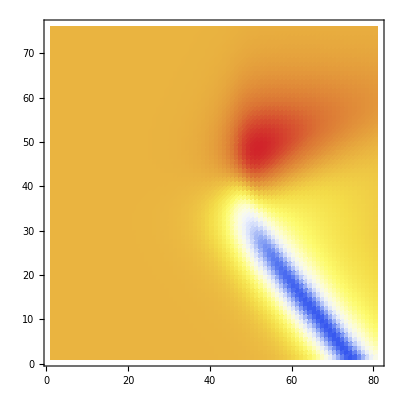

```mathematica
ListDensityPlot[retioTable, PlotRange->All, ColorFunction->"TemperatureMap"
]
```